```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/ps/images

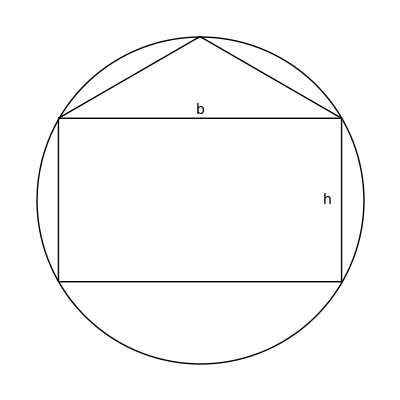

```mathematica
θ=Pi/6;
b= Cos[θ];a=Sin[θ];
fig2={Circle[],Line[{{b,a},{-b,a},{-b,-a},{b,-a},{b,a}}],Line[{{b,a},{0,1},{-b,a}}],Text[Style["b",{14,Italic}],{0,1.1a}],Text[Style["h",{14,Italic}],{0.9 b,0}]}//Graphics
```

```mathematica
Export["fig-geometry2.png",fig2,"PNG"]
```

fig-geometry2.png

```mathematica
g[x_]:=Sqrt[1-x^2]
```

```mathematica
a=0.7;Graphics[{Circle[],Line[{{1,0},{a,g[a]},{-a,g[a]},{-1,0},{1,0}}],Dashing[{0.02,0.01}],Line[{{0,1},{-g[a],-a},{g[a],-a},{0,1}}]}]//Export["fig_trap_tri.png",#,"PNG"]&
```

fig_trap_tri.png